```mathematica
Integrate[2/a Sin[k π  x/a]^2,{x,0,a},Assumptions-> {k ∈ Integers,k>0,a>0}]
```

1-Sin[2 k π]/(2 k π)

```mathematica
Integrate[2/a Sin[k π  x/a] x Sin[l π x/a],{x,0,a},Assumptions-> {k ∈ Integers,l ∈ Integers,a>0}]
```

1/((k-l)^2 (k+l)^2 π^2)2 a (-2 k l-l (-k^2+l^2) π Cos[l π] Sin[k π]+k^2 Sin[k π] Sin[l π]+l^2 Sin[k π] Sin[l π]+Cos[k π] (2 k l Cos[l π]+k (-k^2+l^2) π Sin[l π]))

```mathematica
mE=FullSimplify[%,Assumptions-> {k ∈ Integers,l ∈ Integers,k>l,a>0}]
```

(4 (-1+(-1)^(k+l)) a k l)/((k^2-l^2)^2 π^2)

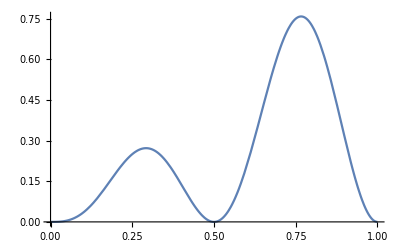

```mathematica
Plot[x Sin[2π x] Sin[2π x],{x,0,1}]
```

```mathematica
ListPointPlot3D[Table[mE /. a->1, {k,1,10},{l,1,10}]]
```

Power::infy: Infinite expression 1/0^2 encountered.

Infinity::indet: Indeterminate expression (0 a ComplexInfinity)/π^2 encountered.

Power::infy: Infinite expression 1/0^2 encountered.

Infinity::indet: Indeterminate expression (0 a ComplexInfinity)/π^2 encountered.

Power::infy: Infinite expression 1/0^2 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression (0 a ComplexInfinity)/π^2 encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

-Graphics3D-